# Quantum Error-Correction Codes

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Elementary Examples: Nine-Qubit Code

### Bit-Flip Errors

Suppose that we want to encode a single-qubit state to protect it against the bit-flip error.

```mathematica
vec=ProductState[S[1]->{c[0],c[1]},"Label"->Ket[ψ]]
```

(c_0 0+c_1 1)_S_1

The encoding is achieved by a quantum circuit model of the form.

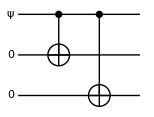

```mathematica
qc=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[1],S[3]]]
```

```mathematica
out=DefaultForm@ExpressionFor[qc];
out//LogicalForm
```

c_0 0_S_10_S_20_S_3+c_1 1_S_11_S_21_S_3

Here is another quantum circuit model giving the same encoding.

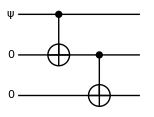

```mathematica
qc2=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[2],S[3]]]
```

```mathematica
out2=DefaultForm@ExpressionFor[qc2];
out2//LogicalForm
```

c_0 0_S_10_S_20_S_3+c_1 1_S_11_S_21_S_3

Consider a bit-flip error occurs randomly

```mathematica
errors=Join[{1},S[{1,2,3},1]]
opE=RandomChoice[errors]
new=opE**out;
new//LogicalForm
```

{1,S_1^x,S_2^x,S_3^x}

S_1^x

c_1 0_S_11_S_21_S_3+c_0 1_S_10_S_20_S_3

This gives the error syndrome.

```mathematica
{(S[1,3]**S[2,3]**new)/new,
(S[2,3]**S[3,3]**new)/new}//Simplify
```

{-1,1}

### Phase-Flip Errors

Suppose that we want to encode a single-qubit state to protect it against the phase-flip error.

```mathematica
vec=ProductState[S[1]->{c[0],c[1]},"Label"->Ket[ψ]]
```

(c_0 0+c_1 1)_S_1

The encoding is achieved by a quantum circuit model of the form.

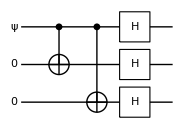

```mathematica
qc=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[1],S[3]],S[{1,2,3},6]]
```

```mathematica
out=DefaultForm@ExpressionFor[qc];
out//LogicalForm
```

((c_0+c_1) 0_S_10_S_20_S_3)/(2 √2)+((c_0-c_1) 0_S_10_S_21_S_3)/(2 √2)+((c_0-c_1) 0_S_11_S_20_S_3)/(2 √2)+((c_0+c_1) 0_S_11_S_21_S_3)/(2 √2)+((c_0-c_1) 1_S_10_S_20_S_3)/(2 √2)+((c_0+c_1) 1_S_10_S_21_S_3)/(2 √2)+((c_0+c_1) 1_S_11_S_20_S_3)/(2 √2)+((c_0-c_1) 1_S_11_S_21_S_3)/(2 √2)

To compare the above result with the desired state, let us construct the encoding explicitly.

```mathematica
new=ProductState[S@{1,2,3}->{1,1}/Sqrt[2]]c[0]+ProductState[S@{1,2,3}->{1,-1}/Sqrt[2]]c[1]
```

c_1 (0/(√2)-1/(√2))_S_1⊗(0/(√2)-1/(√2))_S_2⊗(0/(√2)-1/(√2))_S_3+c_0 (0/(√2)+1/(√2))_S_1⊗(0/(√2)+1/(√2))_S_2⊗(0/(√2)+1/(√2))_S_3

```mathematica
out-new//Elaborate
```

0

Here is another quantum circuit model giving the same encoding.

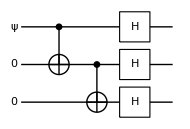

```mathematica
qc2=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[2],S[3]],S[{1,2,3},6]]
```

```mathematica
out2=DefaultForm@ExpressionFor[qc2];
out2//LogicalForm
```

((c_0+c_1) 0_S_10_S_20_S_3)/(2 √2)+((c_0-c_1) 0_S_10_S_21_S_3)/(2 √2)+((c_0-c_1) 0_S_11_S_20_S_3)/(2 √2)+((c_0+c_1) 0_S_11_S_21_S_3)/(2 √2)+((c_0-c_1) 1_S_10_S_20_S_3)/(2 √2)+((c_0+c_1) 1_S_10_S_21_S_3)/(2 √2)+((c_0+c_1) 1_S_11_S_20_S_3)/(2 √2)+((c_0-c_1) 1_S_11_S_21_S_3)/(2 √2)

### Nine-Qubit Code

Here is a widely known quantum circuit model for Shor’s 9-qubit quantum error correction code.

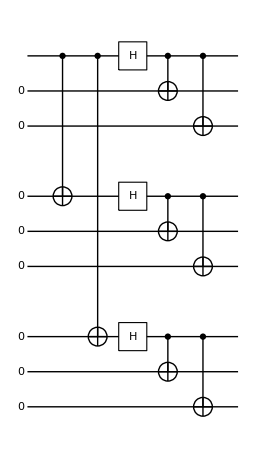

```mathematica
qc=QuantumCircuit[
LogicalForm[Ket[],S@Range[2,9]],
CNOT[S[1],S[4]],CNOT[S[1],S[7]],
S[{1,4,7},6],
{CNOT[S[1],S[2]],CNOT[S[4],S[5]],CNOT[S[7],S[8]]},
{CNOT[S[1],S[3]],CNOT[S[4],S[6]],CNOT[S[7],S[9]]},
"Invisible"->S@{3.5,6.5}
]
```

This is the logical basis state 0of the 9-qubit code.

```mathematica
out0=ExpressionFor@QuantumCircuit[Ket[S[1]->0],qc];
KetFactor@LogicalForm[out0,S@Range[9]]
```

((0_S_10_S_20_S_3+1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6+1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9+1_S_71_S_81_S_9))/(2 √2)

This is the logical basis state 1of the 9-qubit code.

```mathematica
out1=ExpressionFor@QuantumCircuit[Ket[S[1]->1],qc];
KetFactor@LogicalForm[out1,S@Range[9]]
```

((0_S_10_S_20_S_3-1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6-1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9-1_S_71_S_81_S_9))/(2 √2)

Here is another equivalent implementation of Shor’s 9-qubit quantum error correction code.

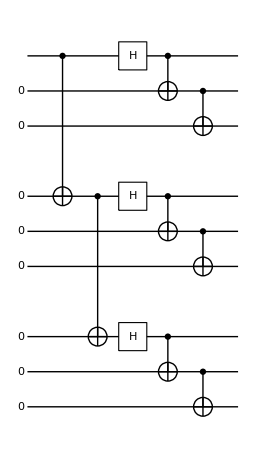

```mathematica
qc=QuantumCircuit[
LogicalForm[Ket[],S@Range[2,9]],
CNOT[S[1],S[4]],CNOT[S[4],S[7]],
S[{1,4,7},6],
{CNOT[S[1],S[2]],CNOT[S[4],S[5]],CNOT[S[7],S[8]]},
{CNOT[S[2],S[3]],CNOT[S[5],S[6]],CNOT[S[8],S[9]]},
"Invisible"->S@{3.5,6.5}
]
```

This is the logical basis state 0of the 9-qubit code.

```mathematica
out0=ExpressionFor@QuantumCircuit[Ket[S[1]->0],qc];
KetFactor@LogicalForm[out0,S@Range[9]]
```

((0_S_10_S_20_S_3+1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6+1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9+1_S_71_S_81_S_9))/(2 √2)

This is the logical basis state 1of the 9-qubit code.

```mathematica
out1=ExpressionFor@QuantumCircuit[Ket[S[1]->1],qc];
KetFactor@LogicalForm[out1,S@Range[9]]
```

((0_S_10_S_20_S_3-1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6-1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9-1_S_71_S_81_S_9))/(2 √2)

## Quantum Error-Correction Conditions

## Stabilizer Formalism

Consider one of the Bell states.

```mathematica
ket=BellState[S@{1,2},3];
ket//LogicalForm
```

(0_S_10_S_2-1_S_11_S_2)/(√2)

```mathematica
grp={1, -S[1,1]**S[2,1],S[1,3]**S[2,3],S[1,2]**S[2,2]};
PauliForm[grp]
```

{I⊗I,-(X⊗X),Z⊗Z,Y⊗Y}

```mathematica
new=grp**ket;
new//LogicalForm
```

{(0_S_10_S_2)/(√2)-(1_S_11_S_2)/(√2),(0_S_10_S_2)/(√2)-(1_S_11_S_2)/(√2),(0_S_10_S_2)/(√2)-(1_S_11_S_2)/(√2),(0_S_10_S_2)/(√2)-(1_S_11_S_2)/(√2)}

Consider the code space 𝒱 of the bit-flip correction code. It is spanned by the following two logical basis states.

```mathematica
ss=S[{1,2,3},None];
bs={Ket[],Ket[S@{1,2,3}->1]};
bs//LogicalForm
```

{0_S_10_S_20_S_3,1_S_11_S_21_S_3}

The stabilizer 𝒮 of 𝒱 is given as follows.

```mathematica
grp={1,S[1,3]**S[2,3],S[2,3]**S[3,3],S[1,3]**S[3,3]};
grp//PauliForm
```

{I⊗I⊗I,Z⊗Z⊗I,I⊗Z⊗Z,Z⊗I⊗Z}

This checks the above group indeed stabilizes 𝒱.

```mathematica
grp**bs[[1]]//LogicalForm[#,ss]&
grp**bs[[2]]//LogicalForm[#,ss]&
```

{0_S_10_S_20_S_3,0_S_10_S_20_S_3,0_S_10_S_20_S_3,0_S_10_S_20_S_3}

{1_S_11_S_21_S_3,1_S_11_S_21_S_3,1_S_11_S_21_S_3,1_S_11_S_21_S_3}

Consider the code space of the phase-flip correction code. It is spanned by the following two logical basis states.

```mathematica
ss=S[{1,2,3},None];
bs={ProductState[ss->{1,1}/Sqrt[2]],ProductState[ss->{1,-1}/Sqrt[2]]};
bs//LogicalForm
```

{(0/(√2)+1/(√2))_S_1⊗(0/(√2)+1/(√2))_S_2⊗(0/(√2)+1/(√2))_S_3,(0/(√2)-1/(√2))_S_1⊗(0/(√2)-1/(√2))_S_2⊗(0/(√2)-1/(√2))_S_3}

The stabilizer 𝒮 of 𝒱 is given as follows.

```mathematica
grp={1,S[1,1]**S[2,1],S[2,1]**S[3,1],S[1,1]**S[3,1]};
grp//PauliForm
```

{I⊗I⊗I,X⊗X⊗I,I⊗X⊗X,X⊗I⊗X}

This checks the above group indeed stabilizes 𝒱.

```mathematica
grp**bs[[1]]//Elaborate//KetFactor//LogicalForm[#,ss]&
```

{((0_S_1+1_S_1)⊗(0_S_2+1_S_2)⊗(0_S_3+1_S_3))/(2 √2),((0_S_1+1_S_1)⊗(0_S_2+1_S_2)⊗(0_S_3+1_S_3))/(2 √2),((0_S_1+1_S_1)⊗(0_S_2+1_S_2)⊗(0_S_3+1_S_3))/(2 √2),((0_S_1+1_S_1)⊗(0_S_2+1_S_2)⊗(0_S_3+1_S_3))/(2 √2)}

```mathematica
grp**bs[[2]]//Elaborate//KetFactor//LogicalForm[#,ss]&
```

{((0_S_1-1_S_1)⊗(0_S_2-1_S_2)⊗(0_S_3-1_S_3))/(2 √2),((0_S_1-1_S_1)⊗(0_S_2-1_S_2)⊗(0_S_3-1_S_3))/(2 √2),((0_S_1-1_S_1)⊗(0_S_2-1_S_2)⊗(0_S_3-1_S_3))/(2 √2),((0_S_1-1_S_1)⊗(0_S_2-1_S_2)⊗(0_S_3-1_S_3))/(2 √2)}

### Pauli Group

Here is the Pauli group on a single qubit.

```mathematica
grp=PauliGroup[1]
```

PauliGroup[1]

```mathematica
elm=GroupElements[grp];
PauliForm[elm]
```

{I,X,Y,Z,-I,-X,-Y,-Z,ⅈ I,ⅈ X,ⅈ Y,ⅈ Z,-ⅈ I,-ⅈ X,-ⅈ Y,-ⅈ Z}

The number of elements quickly increases with the number of qubits.

```mathematica
grp=PauliGroup[2]
```

PauliGroup[2]

```mathematica
elm=GroupElements[grp];
PauliForm[elm]
```

{I⊗I,I⊗X,I⊗Y,I⊗Z,X⊗I,X⊗X,X⊗Y,X⊗Z,Y⊗I,Y⊗X,Y⊗Y,Y⊗Z,Z⊗I,Z⊗X,Z⊗Y,Z⊗Z,-(I⊗I),-(I⊗X),-(I⊗Y),-(I⊗Z),-(X⊗I),-(X⊗X),-(X⊗Y),-(X⊗Z),-(Y⊗I),-(Y⊗X),-(Y⊗Y),-(Y⊗Z),-(Z⊗I),-(Z⊗X),-(Z⊗Y),-(Z⊗Z),ⅈ I⊗I,ⅈ I⊗X,ⅈ I⊗Y,ⅈ I⊗Z,ⅈ X⊗I,ⅈ X⊗X,ⅈ X⊗Y,ⅈ X⊗Z,ⅈ Y⊗I,ⅈ Y⊗X,ⅈ Y⊗Y,ⅈ Y⊗Z,ⅈ Z⊗I,ⅈ Z⊗X,ⅈ Z⊗Y,ⅈ Z⊗Z,-ⅈ I⊗I,-ⅈ I⊗X,-ⅈ I⊗Y,-ⅈ I⊗Z,-ⅈ X⊗I,-ⅈ X⊗X,-ⅈ X⊗Y,-ⅈ X⊗Z,-ⅈ Y⊗I,-ⅈ Y⊗X,-ⅈ Y⊗Y,-ⅈ Y⊗Z,-ⅈ Z⊗I,-ⅈ Z⊗X,-ⅈ Z⊗Y,-ⅈ Z⊗Z}

```mathematica
GroupOrder@grp
```

64

Groups can be conveniently described by the use of generators.

```mathematica
grp=PauliGroup[1]
```

PauliGroup[1]

For example, the single-qubit Pauli group is generated by three Pauli operators.

```mathematica
gnr=GroupGenerators[grp];
PauliForm[gnr]
```

{X,Y,Z}

Here is a generating set of the Pauli group on two qubits. Six generators are enough to generate it.

```mathematica
gnr=GroupGenerators[PauliGroup[2]];
PauliForm[gnr]
```

{I⊗X,I⊗Y,I⊗Z,X⊗I,Y⊗I,Z⊗I}

Pauli group has two extremely useful properties. These are illustrated here.

To avoid the irrelevant phase factors ±1 and ±ⅈ, we play with simple tensor products of single-qubit Pauli operators rather than the full Pauli group.

```mathematica
ops=Flatten@Outer[Multiply,S[1,Full],S[2,Full]]
```

{S_2^0,S_2^x,S_2^y,S_2^z,S_1^x,S_1^x S_2^x,S_1^x S_2^y,S_1^x S_2^z,S_1^y,S_1^y S_2^x,S_1^y S_2^y,S_1^y S_2^z,S_1^z,S_1^z S_2^x,S_1^z S_2^y,S_1^z S_2^z}

```mathematica
PauliForm[ops]
```

{I⊗I,I⊗X,I⊗Y,I⊗Z,X⊗I,X⊗X,X⊗Y,X⊗Z,Y⊗I,Y⊗X,Y⊗Y,Y⊗Z,Z⊗I,Z⊗X,Z⊗Y,Z⊗Z}

This table shows that the elements of the Pauli group either commute or anti-commute with each other.

```mathematica
mat=Outer[GottesmanTest,ops,ops];
TableForm[mat[[-6;;,-6;;]],TableHeadings->{PauliForm@ops[[-6;;]],PauliForm@ops[[-6;;]]},TableAlignments->Right]
```

| Y⊗Y | Y⊗Z | Z⊗I | Z⊗X | Z⊗Y | Z⊗Z
Y⊗Y | 1 | -1 | -1 | 1 | -1 | 1
Y⊗Z | -1 | 1 | -1 | 1 | 1 | -1
Z⊗I | -1 | -1 | 1 | 1 | 1 | 1
Z⊗X | 1 | 1 | 1 | 1 | -1 | -1
Z⊗Y | -1 | 1 | 1 | -1 | 1 | -1
Z⊗Z | 1 | -1 | 1 | -1 | -1 | 1

The rule is also simple that allows to determine which elements commute and which elements anti-commute .

Any element of the Pauli group squares to ±1. Elements with the phase factor ±ⅈ squares to -1.

```mathematica
elm=GroupElements[PauliGroup[S@{1,2}]];
sqr=Map[#**#&,elm];
TableForm[{PauliForm[elm][[-8;;]],sqr[[-8;;]]}]
```

-ⅈ Y⊗I | -ⅈ Y⊗X | -ⅈ Y⊗Y | -ⅈ Y⊗Z | -ⅈ Z⊗I | -ⅈ Z⊗X | -ⅈ Z⊗Y | -ⅈ Z⊗Z
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1

The above property implies that any element of the Pauli group has eigenvalues ±1 or ±ⅈ.

Ignoring the phase factors in the operators of Pauli group, we are dealing with the factor group of the Pauli group with respect to the center {I, -I, ⅈI, -ⅈI}.

```mathematica
op=-I*S[1,2]**S[3,1]**S[4,3]
PauliForm[op,ss=S@{1,2,3,4}]
```

-ⅈ S_1^y S_3^x S_4^z

-ⅈ Y⊗I⊗X⊗Z

This gives the Gottesman vector of the above operator (more precisely, the coset represented by the operator).

```mathematica
vec=GottesmanVector[op,ss]
```

{1,1,0,0,1,0,0,1}

An operator representing the coset is recovered.

```mathematica
new=FromGottesmanVector[vec,ss]
```

S_1^y S_3^x S_4^z

### Properties of Stabilizers

### Unitary Gates in the Stabilizer Formalism

### Clifford Group

The single-qubit Clifford group is rather simple. It is generated by the Hadamard gate and the quadrant phase gate.

```mathematica
gnr=GroupGenerators@CliffordGroup[S]
```

{S^H,S^S}

In fact, it is equivalent to the point group D_3. The point group consists of the six symmetry transformation {I, Mx, My, Mz, R, R**R}.

```mathematica
My=Elaborate@S[6];
Mz=Elaborate@S[7];
Mx=Mz**My**Dagger[Mz];
R=My**Dagger[Mz];
```

Note that the conjugation (not to be confused with conjugate) by an operator is a special case of supermap with a single unitary Kraus element.

```mathematica
Conjugation[op_]:=Supermap[op]
```

Take a look how the Pauli operators transform under the conjugation by single-qubit operations in the Clifford group.

```mathematica
ops={S[1],S[2],S[3]};
Thread[ops->Conjugation[Mx]@ops]//PauliForm//TableForm
Thread[ops->Conjugation[My]@ops]//PauliForm//TableForm
Thread[ops->Conjugation[Mz]@ops]//PauliForm//TableForm
```

X→-X
Y→Z
Z→Y

X→Z
Y→-Y
Z→X

X→Y
Y→-X
Z→Z

```mathematica
Thread[ops->Conjugation[R]@ops]//PauliForm//TableForm
Thread[ops->Conjugation[R**R]@ops]//PauliForm//TableForm
```

X→Y
Y→Z
Z→X

X→Z
Y→X
Z→Y

Here demonstrated is the correspondence between one-to-one mappings ℤ_4×ℤ_4→ℤ_4×ℤ_4 and the two-qubit operations in the Clifford group.

```mathematica
gnr=CNOT[S[1],S[2]]
```

CNOT[{S_1},{S_2}]

Under the conjugation by the CNOT gate, the Pauli operators transform as the following.

```mathematica
ops=Multiply@@@Tuples@{S[1,Full],S[2,Full]};
Timing[new=Elaborate@Thread[ops->Conjugation[gnr]@ops];]
new[[2;;;;4]]//PauliForm//TableForm
```

{0.124038,Null}

I⊗X→I⊗X
X⊗X→X⊗I
Y⊗X→Y⊗I
Z⊗X→Z⊗X

Combinations of the CNOT, Hadamard, and quadrant phase gates generate all transformations preserving the Pauli group. Here is one example.

```mathematica
gnr=CNOT[S[1],S[2]]**S[1,6]**Dagger[S[1,7]]**S[2,7]//Elaborate;
ops={S[1,1],S[2,1],S[1,3],S[2,3]};
```

```mathematica
Thread[ops->Conjugation[gnr]@ops]//PauliForm//TableForm
```

X⊗I→Y⊗X
I⊗X→Z⊗Y
Z⊗I→X⊗X
I⊗Z→Z⊗Z

### Measurement in the Stabilizer Formalism

### Examples

We discuss again quantum teleportation, this time, in the stabilizer formalism.

```mathematica
Let[Complex,c]
in=ProductState[S[3]->c@{0,1},"Label"->Ket[ψ]]
```

(c_0 0+c_1 1)_S_3

This is a quantum circuit model for quantum teleportation. It consists of three stages separated by the vertical dashed lines in the quantum circuit model. The first stage is to share the entangled pair of qubits. The second in the middle corresponds to the Bell measurement. The final stage transmits the measurement outcomes to Alice, and Alice adjusts the state of her qubit according to the classical information.

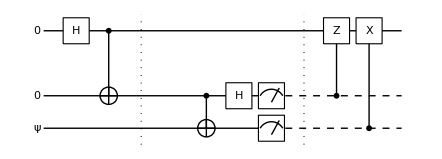

```mathematica
qc=QuantumCircuit[in,LogicalForm[Ket[],S@{1,2}],S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",CNOT[S[2],S[3]],S[2,6],{Measurement[S[2]],Measurement[S[3]]},"Separator",ControlledU[S[2],S[1,3]],ControlledU[S[3],S[1,1]],"Invisible"->S[1.5]]
```

This rearranges the quantum circuit elements to re-analyze the quantum circuit model in stabilizer formalism.

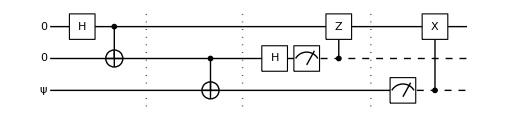

```mathematica
qc2=QuantumCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],"Separator",
S[2,6],Measurement[S[2]],ControlledU[S[2],S[1,3]],"Separator",
Measurement[S[3]],ControlledU[S[3],S[1,1]]
]
```

Now we test the result by performing the quantum circuit model many times.

```mathematica
out=Table[ExpressionFor[qc2],{4}]/.c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1;
LogicalForm@KetFactor[#,S@{2,3}]&/@out//TableForm
```

0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)

Each time the final state on the first qubit is the same regardless of the outcome of the measurements on the second and third qubit.

```mathematica
out=Table[ExpressionFor[qc2],{4}]/.c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1;
LogicalForm@KetFactor[#,S@{2,3}]&/@out//TableForm
```

1_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)

```mathematica
out=Table[ExpressionFor[qc2],{4}]/.c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1;
LogicalForm@KetFactor[#,S@{2,3}]&/@out//TableForm
```

0_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
0_S_20_S_3⊗(c_0 0_S_1+c_1 1_S_1)
1_S_21_S_3⊗(c_0 0_S_1+c_1 1_S_1)

Here we investigate the procedure to remotely implement a CNOT gate.

This is the quantum circuit model we want to analyze.

```mathematica
qc=QuantumCircuit[S[2,6],CNOT[S[2],S[3]],"Separator","Spacer",
{CNOT[S[1],S[2]],CNOT[S[3],S[4]]},
Measurement[S[2]],CNOT[S[2],S@{3,4}],
S[3,6],Measurement[S[3]],ControlledU[S[3],S[1,3]]];
```

This is the general form of the input state.

```mathematica
Let[Integer,x,m]
in=LogicalForm[Ket[S[1]->x[1],S[4]->x[4]],S@{1,2,3,4}];
```

This is the expected form of the output state.

```mathematica
out=Ket[S[1]->x[1],S@{2,3}->m@{2,3},S[4]->Mod[x[1]+x[4],2]];
```

This shows the quantum circuit model with the expected output states specified.

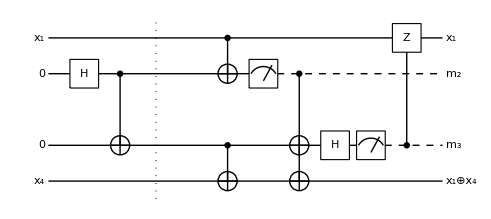

```mathematica
qc1=QuantumCircuit[in,qc,out,"PortSize"->{0.65,2},"Invisible"->S[2.5]]
```

Check whether the quantum circuit model works as expected.

```mathematica
bs=Basis[S@{1,4}];
new=qc**bs;
Thread[LogicalForm[bs]->LogicalForm[new,S@{1,2,3,4}]]//TableForm
```

0_S_10_S_4→0_S_11_S_21_S_30_S_4
0_S_11_S_4→0_S_11_S_20_S_31_S_4
1_S_10_S_4→1_S_11_S_21_S_31_S_4
1_S_11_S_4→1_S_10_S_20_S_30_S_4

## Stabilizer Codes

### Bit-Flip Code

Here are the generators of the stabilizer of the code space for the bit-flip correction code.

```mathematica
gnr={S[1,3]**S[2,3],S[2,3]**S[3,3]};
gnr//PauliForm
```

{Z⊗Z⊗I,I⊗Z⊗Z}

These are error operators correctable by the code.

```mathematica
err={1,S[1,1],S[2,1],S[3,1]};
err//PauliForm
```

{I⊗I⊗I,X⊗I⊗I,I⊗X⊗I,I⊗I⊗X}

```mathematica
chk=Union[Multiply@@@Choices[err,{2}]];
chk//PauliForm
```

{I⊗I⊗I,X⊗X⊗I,X⊗I⊗X,I⊗X⊗X,X⊗I⊗I,I⊗X⊗I,I⊗I⊗X}

Check and confirm that the errors are indeed correctable. To do it, we use GottesmanTest.

```mathematica
?GottesmanTest
```

As one can see, there is only one combination, I⊗I⊗I, of the error operators that commutes with all generators of the stabilizer. But it belongs to the stabilizer.

```mathematica
mat=Outer[GottesmanTest,gnr,chk];
TableForm[mat,TableHeadings->{PauliForm@gnr,PauliForm@chk},TableAlignments->Right]
```

| I⊗I⊗I | X⊗X⊗I | X⊗I⊗X | I⊗X⊗X | X⊗I⊗I | I⊗X⊗I | I⊗I⊗X
Z⊗Z⊗I | 1 | 1 | -1 | -1 | -1 | -1 | 1
I⊗Z⊗Z | 1 | -1 | -1 | 1 | 1 | -1 | -1

This table displays the error syndrome of the bit-flip correction code.

```mathematica
syndrome=Map[(#**gnr**#)/gnr&,err];
TableForm[syndrome,TableAlignments->Right,TableHeadings->{PauliForm@err,PauliForm@gnr}]
```

| Z⊗Z⊗I | I⊗Z⊗Z
I⊗I⊗I | 1 | 1
X⊗I⊗I | -1 | 1
I⊗X⊗I | -1 | -1
I⊗I⊗X | 1 | -1

### Phase-Flip Code

Here are the generators of the stabilizer of the code space for the bit-flip correction code.

```mathematica
gnr={S[1,1]**S[2,1],S[2,1]**S[3,1]};
gnr//PauliForm
```

{X⊗X⊗I,I⊗X⊗X}

These are error operators correctable by the code.

```mathematica
err={1,S[1,3],S[2,3],S[3,3]};
err//PauliForm
```

{I⊗I⊗I,Z⊗I⊗I,I⊗Z⊗I,I⊗I⊗Z}

```mathematica
chk=Union[Multiply@@@Choices[err,{2}]];
chk//PauliForm
```

{I⊗I⊗I,Z⊗Z⊗I,Z⊗I⊗Z,I⊗Z⊗Z,Z⊗I⊗I,I⊗Z⊗I,I⊗I⊗Z}

Check and confirm that the errors are indeed correctable. As one can see, there is only one combination, I⊗I⊗I, of the error operators that commutes with all generators of the stabilizer. But it belongs to the stabilizer.

```mathematica
mat=Outer[GottesmanTest,gnr,chk];
TableForm[mat,TableHeadings->{PauliForm@gnr,PauliForm@chk},TableAlignments->Right]
```

| I⊗I⊗I | Z⊗Z⊗I | Z⊗I⊗Z | I⊗Z⊗Z | Z⊗I⊗I | I⊗Z⊗I | I⊗I⊗Z
X⊗X⊗I | 1 | 1 | -1 | -1 | -1 | -1 | 1
I⊗X⊗X | 1 | -1 | -1 | 1 | 1 | -1 | -1

This table displays the error syndrome of the phase-flip correction code.

```mathematica
syndrome=Map[(#**gnr**#)/gnr&,err];
TableForm[syndrome,TableAlignments->Right,TableHeadings->{PauliForm@err,PauliForm@gnr}]
```

| X⊗X⊗I | I⊗X⊗X
I⊗I⊗I | 1 | 1
Z⊗I⊗I | -1 | 1
I⊗Z⊗I | -1 | -1
I⊗I⊗Z | 1 | -1

### Nine-Qubit Code

Shor’s code needs 9 qubits to encode physical single-qubit quantum states.

```mathematica
jj=Range[9];
```

This is a generating set of the stabilizer of the code.

```mathematica
gnr={
S[1,3]**S[2,3],S[2,3]**S[3,3],
S[4,3]**S[5,3],S[5,3]**S[6,3],
S[7,3]**S[8,3],S[8,3]**S[9,3],
Multiply@@S[{1,2,3,4,5,6},1],
Multiply@@S[{4,5,6,7,8,9},1]}
```

{S_1^z S_2^z,S_2^z S_3^z,S_4^z S_5^z,S_5^z S_6^z,S_7^z S_8^z,S_8^z S_9^z,S_1^x S_2^x S_3^x S_4^x S_5^x S_6^x,S_4^x S_5^x S_6^x S_7^x S_8^x S_9^x}

These are logical operators of the code.

```mathematica
opX=Multiply@@S[jj,1]
opZ=Multiply@@S[jj,3]
```

S_1^x S_2^x S_3^x S_4^x S_5^x S_6^x S_7^x S_8^x S_9^x

S_1^z S_2^z S_3^z S_4^z S_5^z S_6^z S_7^z S_8^z S_9^z

These are the error operators correctable by the code.

```mathematica
err=Prepend[S[jj,All],1]
```

{1,S_1^x,S_1^y,S_1^z,S_2^x,S_2^y,S_2^z,S_3^x,S_3^y,S_3^z,S_4^x,S_4^y,S_4^z,S_5^x,S_5^y,S_5^z,S_6^x,S_6^y,S_6^z,S_7^x,S_7^y,S_7^z,S_8^x,S_8^y,S_8^z,S_9^x,S_9^y,S_9^z}

In order to check that the above errors are indeed correctable, we consider combinations of two error operators.

```mathematica
chk=Union[Multiply@@@Choices[err,{2}]];
Length[chk]
```

379

This calculates the commutation of the above combinations with the generators of the stabilizer.

```mathematica
Timing[mat=Outer[GottesmanTest,chk,gnr];]
```

{5.48404,Null}

This displays a part of the commutation relation. One can see that each of them either commutes or anti-commutes with the generators.

```mathematica
TableForm[mat[[;;5,;;6]],TableAlignments->Right,TableHeadings->{chk[[;;5]],gnr}]
```

| S_1^z S_2^z | S_2^z S_3^z | S_4^z S_5^z | S_5^z S_6^z | S_7^z S_8^z | S_8^z S_9^z
1 | 1 | 1 | 1 | 1 | 1 | 1
S_1^x S_2^x | 1 | -1 | 1 | 1 | 1 | 1
S_1^x S_2^y | 1 | -1 | 1 | 1 | 1 | 1
S_1^x S_2^z | -1 | 1 | 1 | 1 | 1 | 1
S_1^x S_3^x | -1 | -1 | 1 | 1 | 1 | 1

The most dangerous case is that the check operator commutes with all of the generators but does not belong to the stabilizer. To check if there is such case, we examine the check operators that commute with all of the generators.

```mathematica
kk=Catenate@MapIndexed[If[ContainsOnly[#1,{1}],#2,Nothing]&,mat]
```

{1,52,55,118,223,226,262,313,316,325}

This shows that such check operators actually belong to the stabilizer. The considered errors are thus correctable by the code.

```mathematica
chk[[kk]]
```

{1,S_1^z S_2^z,S_1^z S_3^z,S_2^z S_3^z,S_4^z S_5^z,S_4^z S_6^z,S_5^z S_6^z,S_7^z S_8^z,S_7^z S_9^z,S_8^z S_9^z}

This table displays a part of the error syndrome of the code.

```mathematica
syndrome=Map[(#**gnr**#)/gnr&,err];
Style[TableForm[syndrome[[;;8]],TableAlignments->Right,TableHeadings->{err,gnr}],Small]
```

| S_1^z S_2^z | S_2^z S_3^z | S_4^z S_5^z | S_5^z S_6^z | S_7^z S_8^z | S_8^z S_9^z | S_1^x S_2^x S_3^x S_4^x S_5^x S_6^x | S_4^x S_5^x S_6^x S_7^x S_8^x S_9^x
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
S_1^x | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
S_1^y | -1 | 1 | 1 | 1 | 1 | 1 | -1 | 1
S_1^z | 1 | 1 | 1 | 1 | 1 | 1 | -1 | 1
S_2^x | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1
S_2^y | -1 | -1 | 1 | 1 | 1 | 1 | -1 | 1
S_2^z | 1 | 1 | 1 | 1 | 1 | 1 | -1 | 1
S_3^x | 1 | -1 | 1 | 1 | 1 | 1 | 1 | 1

### Five-Qubit Code

We consider a code encoded on 5 qubits.

```mathematica
jj=Range[5];
```

Here are the generators of the stabilizer of the five-qubit code.

```mathematica
gnr={
S[1,1]**S[2,3]**S[3,3]**S[4,1],
S[2,1]**S[3,3]**S[4,3]**S[5,1],
S[1,1]**S[3,1]**S[4,3]**S[5,3],
S[1,3]**S[2,1]**S[4,1]**S[5,3]};
PauliForm[gnr]
```

{X⊗Z⊗Z⊗X⊗I,I⊗X⊗Z⊗Z⊗X,X⊗I⊗X⊗Z⊗Z,Z⊗X⊗I⊗X⊗Z}

These are logical operators of the code.

```mathematica
opX=Multiply@@S[jj,1];
PauliForm[opX]
opZ=Multiply@@S[jj,3];
PauliForm[opZ]
```

X⊗X⊗X⊗X⊗X

Z⊗Z⊗Z⊗Z⊗Z

Here are the error operators correctable by the code.

```mathematica
err=Prepend[S[jj,All],1];
PauliForm[err]
```

{I⊗I⊗I⊗I⊗I,X⊗I⊗I⊗I⊗I,Y⊗I⊗I⊗I⊗I,Z⊗I⊗I⊗I⊗I,I⊗X⊗I⊗I⊗I,I⊗Y⊗I⊗I⊗I,I⊗Z⊗I⊗I⊗I,I⊗I⊗X⊗I⊗I,I⊗I⊗Y⊗I⊗I,I⊗I⊗Z⊗I⊗I,I⊗I⊗I⊗X⊗I,I⊗I⊗I⊗Y⊗I,I⊗I⊗I⊗Z⊗I,I⊗I⊗I⊗I⊗X,I⊗I⊗I⊗I⊗Y,I⊗I⊗I⊗I⊗Z}

```mathematica
chk=Union[Multiply@@@Choices[err,{2}]];
Length[chk]
```

121

```mathematica
Timing[mat=Outer[GottesmanTest,chk,gnr];]
```

{1.12877,Null}

This displays a part of the commutation relations of some of the check  operators. One can see that each of them either commutes or anti-commutes with the generators.

```mathematica
TableForm[mat[[;;5]],TableAlignments->Right,TableHeadings->PauliForm@{chk[[;;5]],gnr}]
```

| X⊗Z⊗Z⊗X⊗I | I⊗X⊗Z⊗Z⊗X | X⊗I⊗X⊗Z⊗Z | Z⊗X⊗I⊗X⊗Z
I⊗I⊗I⊗I⊗I | 1 | 1 | 1 | 1
X⊗X⊗I⊗I⊗I | -1 | 1 | 1 | -1
X⊗Y⊗I⊗I⊗I | -1 | -1 | 1 | 1
X⊗Z⊗I⊗I⊗I | 1 | -1 | 1 | 1
X⊗I⊗X⊗I⊗I | -1 | -1 | 1 | -1

The most dangerous case is that the check operator commutes with all of the generators but does not belong to the stabilizer. To check if there is such case, we examine the check operators that commute with all of the generators.

```mathematica
kk=Catenate@MapIndexed[If[ContainsOnly[#1,{1}],#2,Nothing]&,mat]
```

{1}

This shows that such check operators actually belong to the stabilizer. The considered errors are thus correctable by the code.

```mathematica
chk[[kk]]
```

{1}

This shows the error syndrome of the code upon the measurement of the generators of the stabilizer.

```mathematica
syndrome=Map[(#**gnr**#)/gnr&,err];
TableForm[syndrome,TableAlignments->Right,TableHeadings->{PauliForm@err,PauliForm@gnr}]
```

| X⊗Z⊗Z⊗X⊗I | I⊗X⊗Z⊗Z⊗X | X⊗I⊗X⊗Z⊗Z | Z⊗X⊗I⊗X⊗Z
I⊗I⊗I⊗I⊗I | 1 | 1 | 1 | 1
X⊗I⊗I⊗I⊗I | 1 | 1 | 1 | -1
Y⊗I⊗I⊗I⊗I | -1 | 1 | -1 | -1
Z⊗I⊗I⊗I⊗I | -1 | 1 | -1 | 1
I⊗X⊗I⊗I⊗I | -1 | 1 | 1 | 1
I⊗Y⊗I⊗I⊗I | -1 | -1 | 1 | -1
I⊗Z⊗I⊗I⊗I | 1 | -1 | 1 | -1
I⊗I⊗X⊗I⊗I | -1 | -1 | 1 | 1
I⊗I⊗Y⊗I⊗I | -1 | -1 | -1 | 1
I⊗I⊗Z⊗I⊗I | 1 | 1 | -1 | 1
I⊗I⊗I⊗X⊗I | 1 | -1 | -1 | 1
I⊗I⊗I⊗Y⊗I | -1 | -1 | -1 | -1
I⊗I⊗I⊗Z⊗I | -1 | 1 | 1 | -1
I⊗I⊗I⊗I⊗X | 1 | 1 | -1 | -1
I⊗I⊗I⊗I⊗Y | 1 | -1 | -1 | -1
I⊗I⊗I⊗I⊗Z | 1 | -1 | 1 | 1

Let us evaluate explicitly the logical basis states of the code.

From the generating set of the stabilizer given above, we can construct the elements of the stabilizer explicitly.

```mathematica
new=Union@Join[gnr,Multiply@@@Tuples[gnr,2]];
grp=Union@Join[new,Multiply@@@Tuples[new,2]]
Length[grp]
```

{1,S_1^x S_2^x S_3^y S_5^y,S_1^x S_2^y S_4^y S_5^x,S_1^x S_2^z S_3^z S_4^x,S_1^x S_3^x S_4^z S_5^z,S_1^y S_2^x S_3^x S_4^y,S_1^y S_2^y S_3^z S_5^z,S_1^y S_2^z S_4^z S_5^y,S_1^y S_3^y S_4^x S_5^x,S_1^z S_2^x S_4^x S_5^z,S_1^z S_2^y S_3^y S_4^z,S_1^z S_2^z S_3^x S_5^x,S_1^z S_3^z S_4^y S_5^y,S_2^x S_3^z S_4^z S_5^x,S_2^y S_3^x S_4^x S_5^y,S_2^z S_3^y S_4^y S_5^z}

16

Recall that the logical Z operator is given as fallows.

```mathematica
opZ=Multiply@@S[jj,3]
```

S_1^z S_2^z S_3^z S_4^z S_5^z

We now want to get the simultaneous eigenstates of the stabilizer and the logical Z operator.

```mathematica
ops=Append[grp,opZ];
mat=Matrix@Rest@ops;
```

```mathematica
{val,vec}=CommonEigensystem[mat];
Style[TableForm[val[[-5;;]],TableAlignments->Right],Small]
```

1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

We see that the code space is spanned by the last two eigenvectors. The last one belongs to the eigenvalue 1 of the logical Z operator.

```mathematica
bs=Basis[S@jj];
ket0=-vec[[-1]].bs;
ket0//SimpleForm
```

00000/4-00011/4+00101/4-00110/4+01001/4+01010/4-01100/4-01111/4-10001/4+10010/4+10100/4-10111/4-11000/4-11011/4-11101/4-11110/4

```mathematica
ket1=vec[[-2]].bs;
ket1//SimpleForm
```

-1/4 00001-00010/4-00100/4-00111/4-01000/4+01011/4+01101/4-01110/4-10000/4-10011/4+10101/4+10110/4-11001/4+11010/4-11100/4+11111/4

This confirms that they are indeed eigenstates of the logical Z operator with proper eigenvalues.

```mathematica
(opZ**ket0)/ket0
(opZ**ket1)/ket1//Simplify
```

1

-1

This confirms that the logical X operator flips the logical basis states as expected.

```mathematica
opX**ket0/ket1//Simplify
opX**ket1/ket0//Simplify
```

1

1

## Surface Codes

### Toric Codes

Consider a toric code on a 3x3 square lattice on the surface of a torus.

```mathematica
$L=3;
jj=Range[0,$L-1];
```

The qubits on the horizontal and vertical edges are labelled by S and T, respectively.

```mathematica
Let[Qubit,S,T]
```

This defines plaquette operators.

```mathematica
A[{i_,j_}]:=S[i,j,3]**S[i,Mod[j+1,$L],3]**T[i,j,3]**T[Mod[i+1,$L],j,3]
```

Here are the independent plaquette operators.

```mathematica
AA=Most@Flatten@Table[A@{i,j},{i,jj},{j,jj}]
```

{S_(0,0)^z S_(0,1)^z T_(0,0)^z T_(1,0)^z,S_(0,1)^z S_(0,2)^z T_(0,1)^z T_(1,1)^z,S_(0,0)^z S_(0,2)^z T_(0,2)^z T_(1,2)^z,S_(1,0)^z S_(1,1)^z T_(1,0)^z T_(2,0)^z,S_(1,1)^z S_(1,2)^z T_(1,1)^z T_(2,1)^z,S_(1,0)^z S_(1,2)^z T_(1,2)^z T_(2,2)^z,S_(2,0)^z S_(2,1)^z T_(0,0)^z T_(2,0)^z,S_(2,1)^z S_(2,2)^z T_(0,1)^z T_(2,1)^z}

```mathematica
Length[AA]
```

8

This defines vertex operators.

```mathematica
B[{i_,j_}]:=S[i,j,1]**S[Mod[i-1,$L],j,1]**T[i,j,1]**T[i,Mod[j-1,$L],1]
```

Here are the independent vertex operators.

```mathematica
BB=Most@Flatten@Table[B@{i,j},{i,jj},{j,jj}]
```

{S_(0,0)^x S_(2,0)^x T_(0,0)^x T_(0,2)^x,S_(0,1)^x S_(2,1)^x T_(0,0)^x T_(0,1)^x,S_(0,2)^x S_(2,2)^x T_(0,1)^x T_(0,2)^x,S_(0,0)^x S_(1,0)^x T_(1,0)^x T_(1,2)^x,S_(0,1)^x S_(1,1)^x T_(1,0)^x T_(1,1)^x,S_(0,2)^x S_(1,2)^x T_(1,1)^x T_(1,2)^x,S_(1,0)^x S_(2,0)^x T_(2,0)^x T_(2,2)^x,S_(1,1)^x S_(2,1)^x T_(2,0)^x T_(2,1)^x}

```mathematica
Length[BB]
```

8

The plaquette operators commute with vertex operators.

```mathematica
Outer[GottesmanTest,AA,BB]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

Here are two logical Z operators of the code.

```mathematica
opZ={
Multiply@@Table[S[i,1,3],{i,jj}],
Multiply@@Table[T[0,j,3],{j,jj}]
}
```

{S_(0,1)^z S_(1,1)^z S_(2,1)^z,T_(0,0)^z T_(0,1)^z T_(0,2)^z}

```mathematica
Outer[GottesmanTest,opZ,AA]//MatrixForm
Outer[GottesmanTest,opZ,BB]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

Here are two logical X operators of the code.

```mathematica
opX={
Multiply@@Table[T[i,2,1],{i,jj}],
Multiply@@Table[S[1,j,1],{j,jj}]
}
```

{T_(0,2)^x T_(1,2)^x T_(2,2)^x,S_(1,0)^x S_(1,1)^x S_(1,2)^x}

```mathematica
Outer[GottesmanTest,opX,AA]//MatrixForm
Outer[GottesmanTest,opX,BB]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

### Planar Codes

### Recovery Procedure

Here provided is a simple check of the equivalence of two quantum circuit models for local measurement of vertex operators.

```mathematica
$n=4;
jj=Range[$n];
cc=S[jj,None];
tt=S[$n+1,None];
qq=Append[cc,tt];
```

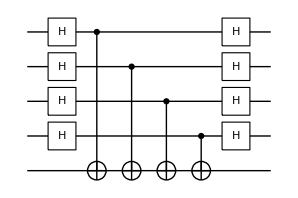

```mathematica
qc1=QuantumCircuit[S[jj,6],Sequence@@Map[CNOT[#,tt]&,cc],S[jj,6]]
```

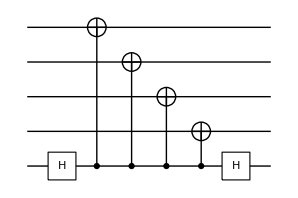

```mathematica
qc2=QuantumCircuit[S[$n+1,6],Sequence@@Flatten@Table[CNOT[S[$n+1],S[j]],{j,jj}],S[$n+1,6]]
```

```mathematica
Elaborate[qc1==qc2]
```

True